```mathematica
Clear["Global`*"]
```

```mathematica
Integrate[x Log[(x+1)/(1-x)],{x,0,1-ϵ},Assumptions->{1>ϵ>0}]+Integrate[x Log[(x+1)/(x-1)],{x,1+ϵ,z},Assumptions->{1>ϵ>0,z>1+ϵ}]
```

1-ϵ+(-2+ϵ) ϵ ArcTanh[1-ϵ]+1/2 (-2+2 z-2 ϵ-2 ArcCoth[z]+z^2 Log[(1+z)/(-1+z)]+ϵ (2+ϵ) Log[ϵ/(2+ϵ)])

```mathematica
Limit[1-ϵ+(-2+ϵ) ϵ ArcTanh[1-ϵ]+1/2 (-2+2 z-2 ϵ-2 ArcCoth[z]+z^2 Log[(1+z)/(-1+z)]+ϵ (2+ϵ) Log[ϵ/(2+ϵ)]),ϵ->0]
```

```mathematica
z-ArcCoth[z]+1/2 z^2 Log[(1+z)/(-1+z)]
```

```mathematica
z-ArcCoth[z]+1/2 z^2 Log[(1+z)/(-1+z)]/.ArcCoth[z]->1/2 Log[(1+z)/(z-1)]//Simplify
```

z+1/2 (-1+z^2) Log[(1+z)/(-1+z)]

```mathematica
Integrate[x Log[(x+1)/(1-x)],{x,0,z},Assumptions->{z<1}]
```

ConditionalExpression[z+(-1+z^2) ArcTanh[z],z≥0]

```mathematica
z+(-1+z^2) ArcTanh[z]/.ArcTanh[z]->1/2 Log[(1+z)/(1-z)]//Simplify
```

z+1/2 (-1+z^2) Log[(1+z)/(1-z)]

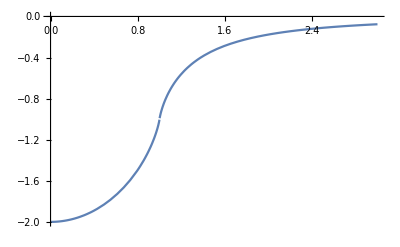

```mathematica
Plot[-(1+(1-y^2)/(2y)Log@Abs[(1+y)/(1-y)]),{y,0,3}]
```

```mathematica
Limit[1+(1-y^2)/(2y)Log@Abs[(1+y)/(1-y)],y->1]
```

1

```mathematica
D[1+(1-y^2)/(2y)Log[(1+y)/(1-y)],y]//FullSimplify
```

1/y-((1+y^2) Log[(1+y)/(1-y)])/(2 y^2)

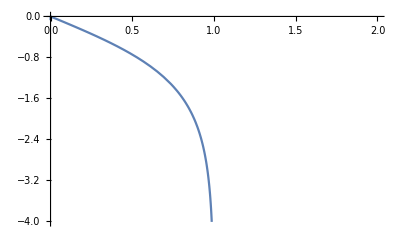

```mathematica
Plot[((1-y) (1-y^2) (1/(1-y)+(1+y)/(1-y)^2))/(2 y (1+y))-Log[(1+y)/(1-y)]-((1-y^2) Log[(1+y)/(1-y)])/(2 y^2),{y,0,2}]
```